# Second Quantization Functions

Core Functionscore | Details and options
Basic Examples(States and Operators)basic1 | Quasi Probability Representations and Examplesquasi
Advanced Examplesadvanced | core

In this Tech Note, we present the implementation of second quantization for bosons within the QuantumFramework, utilizing a truncated Fock space. This approach enables simple manipulation and representation of quantum states, which are essential for a wide range of calculations. By leveraging the core features of the QuantumFramework, we simplify the process of working with common quantum states and operators, facilitating diverse computational tasks in fundamental quantum mechanics and quantum optics.

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`SecondQuantization`
```

### Core Functions

### Fock space size and utilities

SetFockSpaceSize[size] | sets size as the default truncation dimension , after called all the other definitions can use this default size
OperatorVariance[ψ,op] | Variance of the operator op for a state ψ

### States

FockState[n,size] | n-th Fock state in a basis of dimension size
FockState[{n_1,n_2,..},size] | Multimode Fock state with occupation numbers n_i , with each mode in a basis of dimension size 
CoherentState[size]
CoherentState[size][α] | Parametric state representing a non-normalized coherent state in a  basis of dimension size , the complex amplitude is a parameter
ThermalState[nbar,size] | Thermal mixed state with average number of photons nbar in a  basis of dimension size
CatState[size]
CatState[size][α,ϕ] | Parametric general cat state representing a superposition of coherent states in a basis of dimension size, the complex amplitude and the phase are parameters

### Operators

AnnihilationOperator2[size, ord] | Bosonic annihilation operator in a truncated Fock space
with basis dimension size and qudit order ord
DisplacementOperator2[α,size, ord] | Phase space displacement operator of a single mode with complex amplitude alpha , basis dimension size and qudit order ord
SqueezeOperator2[ξ,size,ord] | Squeeze operator of a single mode with complex parameter xi , basis dimension size  and qudit order ord
QuadratureOperators2[size,ord] |  X_1 and X_2 position and momentum quadrature operators with basis dimension size  and qudit order ord
PhaseShiftOperator2[θ,size,ord] | Phase space rotation operator with rotation angle θ, basis dimension size and qudit order ord
BeamSplitterOperator2[{θ,ϕ},size,ord] | Two mode beam-splitter operator, θ indicates the reflectivity, ϕ the relative phase in a basis of dimension size and qudit order ord

We will briefly demonstrate how to apply all these functions in Wolfram quantum framework.

## Details and options

### Operators Mathematical Definitions

DisplacementOperator | Exp[α a^† -α^*a]
SqueezeOperator | Exp[1/2(ξ* a^2 - ξ  a^(†2))]
PhaseShiftOperator | Exp[ⅈ θ a^†a]
BeamSplitterOperator | Exp[θ(ⅇ^(ⅈ ϕ)a_1 a_2^†-ⅇ^(-ⅈ ϕ)a_1^†a_2)]
QuadratureOperators | X_1:1/2(a+a^†)
X_2:1/(2 ⅈ)(a-a^†)

#### Ordering Option

Displacement and Squeeze operators can have different definitions based on operator ordering. We include the "Ordering" option to specify the order (weak , normal or anti normal ). Theoretically  in a infinite dimensional space they are all equivalent , but in a truncated space these operators have numerical error, and depending on the calculation some choice of ordering can be more accurate.

#### Displacement operator ordering

By default when "Ordering" is not specified normal ordering is used, the formulas of the three orders are shown below:

DisplacementOperator[..,"Ordering"→st] | st can be "Normal", "Weak" or "Antinormal".

For "Normal", one gets:
Exp[-|α|^2/2]Exp[α .01 a^†]Exp[-α* a]

For "Weak", one gets:
Exp[α a^†-α*a]

For "Antinormal", one gets:
Exp[|α|^2/2]Exp[-α*a]Exp[α a^†]

#### Squeeze operator ordering

By default when "Ordering" is not specified normal ordering is used, the formulas of the three orders are shown below:

SqueezeOperator[…,"Ordering"→st] | st can be "Normal", "Antinormal" or "Weak". Given  ξ=rⅇ^(ⅈ θ)
for "Normal", one gets:
Exp[-1/2 ⅇ^(ⅈ θ) Tanh[r]a^(†2)]Exp[-Log[Cosh[r]](a^†a + 1/2)] Exp[1/2 ⅇ^(-ⅈ θ)Tanh[r]a^2]

For "Weak", one gets:
Exp[1/2(ξ* a^2 - ξ  a^(†2))]

For "Antinormal", one gets:
Exp[1/2 ⅇ^-ⅈθ Tanh[r]a^2]Exp[Log[Cosh[r]](a^†a + 1/2)] Exp[-1/2 ⅇ^(ⅈ θ)Tanh[r]a^(†2)]

### Basic Examples

#### Setting the space size

Set the default size to 20:

```mathematica
SetFockSpaceSize[20];
```

```mathematica
AnnihilationOperator[]
```

QuantumOperator[…]

Calling it with no arguments, sets again the default size when loading the paclet which is 16:

```mathematica
SetFockSpaceSize[];
```

```mathematica
AnnihilationOperator[]
```

QuantumOperator[…]

#### Annihilation operator

Define an annihilation operator with a given size and uses default order (1):

```mathematica
AnnihilationOperator[8]
```

QuantumOperator[…]

Define an annihilation operator to the second mode with default truncation size:

```mathematica
AnnihilationOperator[{2}]
```

QuantumOperator[…]

Define an annihilation operator with dimension 5  in the third order (or mode):

```mathematica
AnnihilationOperator[5,{3}]
```

QuantumOperator[…]

#### Creation operator and Fock states

Define creation operator just taking the adjoint of the annihilation operator  with "Dagger" property or SuperDagger:

```mathematica
a = AnnihilationOperator[];
SuperDagger[a]@ FockState[1] //TraditionalForm
```

√2 2

#### Multimode Fock State

Create a two mode  Fock state with occupation numbers 2 and 12:

```mathematica
ψ = FockState[{2,12}];
```

```mathematica
ψ["Formula"]
```

212

Apply the annihilation operator to both modes , state|1,11⟩ is expected up to a global constant:

```mathematica
(a["Bend"]@ψ)["Formula"]
```

2 √6111

Equivalent using QuantumState with strings arguments, but  QuantumState with string arguments will not work if one number is bigger than 9( it will interpret it as extra qudits):

```mathematica
FockState[{0,0},5]==QuantumState["00",5]
```

True

#### Coherent state

Symbolic coherent state:

```mathematica
CoherentState[20][β]//TraditionalForm
```

0+β1+β^2/(√2)2+β^3/(√6)3+β^4/(2 √6)4+β^5/(2 √30)5+β^6/(12 √5)6+β^7/(12 √35)7+β^8/(24 √70)8+β^9/(72 √70)9+β^10/(720 √7)10+β^11/(720 √77)11+β^12/(1440 √231)12+β^13/(1440 √3003)13+β^14/(10080 √858)14+β^15/(30240 √1430)15+β^16/(120960 √1430)16+β^17/(120960 √24310)17+β^18/(725760 √12155)18+β^19/(725760 √230945)19

Photon distribution of a coherent state with  α = 1.3+2ⅈ :

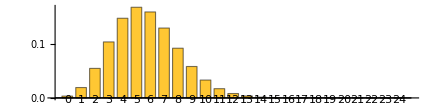

```mathematica
CoherentState[25][1.3+2ⅈ]["Normalize"]["ProbabilityPlot",LabelStyle-> 6,AspectRatio->1/4]
```

#### Cat State

Create a cat state 𝒩_α(α+ⅇ^ⅈϕ-α) of amplitude α=2+ⅈ and ϕ=3π/4:

```mathematica
CatState[25][2+ⅈ,3π/4]
```

QuantumState[…]

Photon distribution of the same state:

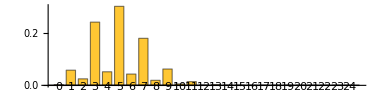

```mathematica
CatState[25][2+ⅈ,3π/4]["ProbabilityPlot",LabelStyle-> 6,AspectRatio->1/4]
```

#### Displacement operator

Create displacement operator of size 40 with amplitude 3+ ⅈ:

```mathematica
DisplacementOperator[3+ⅈ,40]
```

QuantumOperator[QuantumState[SparseArray[<1600>, {1600}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {40}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {40}], {QuditName[2, Dual -> True], 1} -> SparseArray[<1>, {40}], <<35>>, {<<2>>} -> <<1>>, {QuditName[39, Dual -> True], 1} -> SparseArray[<1>, {40}]|>], <<4>>|>]], {<<2>>}]

Create a coherent state displacing the vacuum:

```mathematica
DisplacementOperator[α,40][]==CoherentState[40][α]
```

True

Specify the order(mode) of the operator with default size, second mode in this case:

```mathematica
DisplacementOperator[0.5,{2}]
```

QuantumOperator[…]

### Phase shift operator

Rotation angle θ =0 must be equal to the identity operator:

```mathematica
PhaseShiftOperator[0]==QuantumOperator["I"[$FockSize]]
```

True

Specify the basis size and order:

```mathematica
PhaseShiftOperator[π/4,5,{2}]
```

QuantumOperator[…]

Phase shift operator coincides with the "Z" gate for qudits when the angle is 2π/n (up to conjugation):

```mathematica
With[{n=RandomInteger[{1,$FockSize-1}]},PhaseShiftOperator[2π/n,n]==QuantumOperator["Z"[n]]["Conjugate"]]
```

True

### Squeeze operator

Create squeeze operator of default size with complex parameter 1+ⅈ:

```mathematica
SqueezeOperator[1.+ⅈ]
```

QuantumOperator[…]

Create a squeezed vacuum state of dimension 15 in the second mode (ξ = 0.6), we get the state |0⟩ ⊗ |ξ⟩:

```mathematica
state =SqueezeOperator[0.9,15,{2}]@FockState[{0,0},15]
```

QuantumState[…]

Plot the non-zero amplitudes of the state:

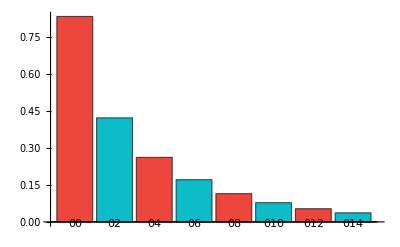

```mathematica
state["AmplitudePlot",ChartLegends->Automatic]
```

### Beam-Splitter Operator

Symmetric beam-splitter setting θ = π/4 and ϕ = π/2:

```mathematica
symmetricBS =BeamSplitterOperator[{π/4.,π/2.}]
```

QuantumOperator[…]

Transform the state |1,1⟩ using the symmetric beam-splitter:

```mathematica
symmetricBS[FockState[{1,1}]]//Chop
```

(0.+0.707107 ⅈ)02+(0.+0.707107 ⅈ)20

Specify the order (where the operator acts) and the basis dimension:

```mathematica
BeamSplitterOperator[{0.2,0.9},6,{1,3}]
```

QuantumOperator[…]

### OperatorVariance

Calculate the variance of the quadrature operators for the ground state:

```mathematica
OperatorVariance[FockState[0],#]& /@ QuadratureOperators[]
```

{1/4,1/4}

A Fock state has a definite number of photons so the variance of the number operator is zero:

```mathematica
a=AnnihilationOperator[];
OperatorVariance[FockState[2],SuperDagger[a]@a]
```

0

#### Quadrature Operators

Compute the commutator of quadrature operators, it is  ⅈ/2 1 the error in the last term is expected behaviour due to truncation:

```mathematica
Commutator@@ QuadratureOperators[]-ⅈ/2 QuantumOperator["I"[$FockSize]]
```

-8 ⅈ1515

Expectation value ⟨ X_1⟩ for Fock state 3 using QuantumMeasurementOperator:

```mathematica
With[{xop = QuadratureOperators[][[1]]},QuantumMeasurementOperator[N@(xop^2)]@FockState[3]]["Mean"]
```

1.75

### Ordering option

Verify displacement operator is unitary using "UnitaryQ" for α = ⅈ, for this task testing with weak ordering is more accurate

```mathematica
DisplacementOperator[1. ⅈ]["UnitaryQ"]
```

False

```mathematica
DisplacementOperator[1.ⅈ,"Ordering"->"Weak"]["UnitaryQ"]
```

True

For a squeezed vacuum state with ξ = 1.5 +0.5 ⅈ and size = 20 compare numerical error of "Weak" and "Normal" to the analytic expression. Using  this value of the complex parameter ξ the truncation dimension is not enough for the weak ordered operator, and the normal ordered one is more accurate

```mathematica
analytic = 1/√Cosh[Abs[ξ]]Table[√((2m)!)/(2^m m!)(-1)^m ⅇ^(ⅈ m Arg[ξ])Tanh[Abs[ξ]]^m,{m,0,9}]/.ξ->(1.5+0.5ⅈ);
```

```mathematica
absoluteErrors= (SqueezeOperator[1.5+0.5ⅈ,20,"Ordering"->#][]["AmplitudeList"]-analytic)& /@{"Normal","Weak"};
```

```mathematica
TableForm[absoluteErrors//Chop//Transpose,TableHeadings->{Table[StringForm["|``⟩",i],{i,0,20,2}], {"Normal","Weak"}}]
```

| Normal | Weak
|0⟩ | 0 | -0.000275202
|2⟩ | 0 | -0.00321923-0.00107308 ⅈ
|4⟩ | 0 | -0.0120623-0.00904674 ⅈ
|6⟩ | 0 | -0.0214194-0.0309391 ⅈ
|8⟩ | 0 | -0.0176372-0.0604703 ⅈ
|10⟩ | 0 | 0.00310254-0.0817001 ⅈ
|12⟩ | 0 | 0.0330558-0.0878983 ⅈ
|14⟩ | 0 | 0.0645373-0.0795701 ⅈ
|16⟩ | 0 | 0.0909739-0.0580024 ⅈ
|18⟩ | 0 | 0.10781-0.027051 ⅈ

### Applications

#### Mean number of photons

```mathematica
ψ = QuantumState["RandomPure",$FockSize];
```

Using QuantumMeasurementOperator:

```mathematica
(QuantumMeasurementOperator[SuperDagger[a]@a][ψ])["Mean"]
```

6.63112

Bracket notation ⟨ ψ |a^†a|ψ⟩ :

```mathematica
Chop["Scalar" // SuperDagger[ψ]@(SuperDagger[a]@a)@ψ ]
```

6.63112

Using the probabilities in the diagonal of the density matrix:

```mathematica
Dot[Range[0,$FockSize-1],Diagonal@ψ["DensityMatrix"]]
```

6.63112+0. ⅈ

#### Heisenberg evolution of annihilation operator

It's well known the annihilation operator in the Heisenberg picture is â(t)=â ⅇ^(-ⅈ ω t) , we can use Superoperators in the framework to describe Heisenberg picture evolution

Define the Hamiltonian:

```mathematica
H = ℏ ω (SuperDagger[a]@a+1/2);
```

Superoperator that allows evolving another operator:

```mathematica
expℋ =MatrixExp[-ⅈ QuantumOperator["Hamiltonian"[H/ℏ]]t];
```

Evolve the operator:

```mathematica
heisenbergAnnihilation =Simplify[expℋ["Dagger"][a["MatrixQuantumState"]]["Operator"],{t,ω}∈ Reals]
```

ⅇ^(-ⅈ t ω)01+√2 ⅇ^(-ⅈ t ω)12+√3 ⅇ^(-ⅈ t ω)23+2 ⅇ^(-ⅈ t ω)34+√5 ⅇ^(-ⅈ t ω)45+√6 ⅇ^(-ⅈ t ω)56+√7 ⅇ^(-ⅈ t ω)67+2 √2 ⅇ^(-ⅈ t ω)78+3 ⅇ^(-ⅈ t ω)89+√10 ⅇ^(-ⅈ t ω)910+√11 ⅇ^(-ⅈ t ω)1011+2 √3 ⅇ^(-ⅈ t ω)1112+√13 ⅇ^(-ⅈ t ω)1213+√14 ⅇ^(-ⅈ t ω)1314+√15 ⅇ^(-ⅈ t ω)1415

Compare the result:

```mathematica
a ⅇ^(-ⅈ ω t)==heisenbergAnnihilation
```

True

### Quasi-probability Representations

Two phase space  quasi-probability representations are included Wigner and HusimiQ , which are used extensively in quantum mechanics and quantum optics.  They are calculated numerically in a grid of phase space points and an interpolating function is returned. Glauber representation is not included because for a general state is not feasible to implement a numerical algorithm , due to the singularities of this representation.

WignerRepresentation[ψ,{xmin,xmax},{pmin,pmax},opts] | Computes the Wigner quasi-probabilty representation of a quantum state ψ , in a phase space rectangular region defined by the given limits of  x and p
HusimiQRepresentation[ψ,{xmin,xmax},{pmin,pmax},opts] | Computes the Husimi Q function representation of a quantum state ψ  , in a phase space rectangular region defined by the given limits of x and p

We will briefly demonstrate how to apply all these functions in Wolfram quantum framework.

### Basic Examples

#### Ground state Wigner Representation:

In the region from -4 to 4:

```mathematica
wig = WignerRepresentation[FockState[0],{-4,4},{-4,4}];
```

```mathematica
Plot3D[
wig[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80
]
```

-Graphics3D-

#### Fock state HusimiQ Representation

Calculate the representation for Fock state with n = 4:

```mathematica
husi = HusimiQRepresentation[FockState[4],{-4,4},{-4,4}];
```

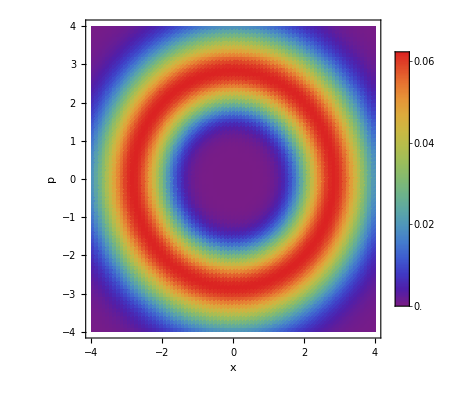

```mathematica
DensityPlot[
husi[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80,
FrameLabel->{"x","p"}
]
```

### Applications

#### Expectation values

We will use the Fock state |2⟩:

```mathematica
wig = WignerRepresentation[FockState[2],{-5,5},{-5,5}];
```

Phase space integral:

```mathematica
NIntegrate[wig[x,p],{x,-4,4},{p,-4,4},AccuracyGoal->2]
```

1.00019

An expectation value calculation ⟨x^4⟩:

```mathematica
NIntegrate[x^4 wig[x,p],{x,-4,4},{p,-4,4},AccuracyGoal->2]
```

9.74831

#### Squeezed vacuum Wigner Representation

This exhibits graphically the non classical behavior of squeezed states regarding the quadratures:

```mathematica
squeezedVacuumFunc = WignerRepresentation[SqueezeOperator[0.5][],{-4,4},{-4,4}];
```

```mathematica
Plot3D[
squeezedVacuumFunc[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"SunsetColors",
PlotRange->All,
PlotLegends->Automatic,
PlotPoints->80
]
```

-Graphics3D-

### Options

"GaussianScaling" | √2 | Scaling factor of the representation
"GridSize" | 100 | Granularity of the sampling

#### Scaling of the representation for ground state

```mathematica
wig = WignerRepresentation[FockState[0],{-4,4},{-4,4},"GaussianScaling"-> 0.5];
```

```mathematica
Rasterize[Plot3D[wig[x,p],{x,-4,4},{p,-4,4},
ColorFunction->"Rainbow",
PlotRange->All,
PlotLegends->Automatic]]
```

-Graphics-

#### Using GridSize

Calculating the value of the Wigner function of Fock state |2⟩ at the origin:

```mathematica
wig = WignerRepresentation[FockState[2],{-6,6},{-6,6},"GridSize"->140];
wig[0,0]
```

0.318182

However, "GridSize" of 20 is not enough for this region and has a lot of numerical error:

```mathematica
wig = WignerRepresentation[FockState[2],{-6,6},{-6,6},"GridSize"->20];
wig[0,0]
```

0.126233

The exact value from analytical expression is:

```mathematica
N[1/π ⅇ^(-(x^2+p^2))LaguerreL[2,2(x^2+p^2)]/.{x->0.08,p->0}]
```

0.31831

## Advanced examples

### Decay of a coherent state

ℋ= ω (â)^†â   with Lindblad jump operator L_1 = √γ â (single photon loss channel), taking ω = 1:

```mathematica
SetFockSpaceSize[15];
α = 2 Exp[I RandomReal[{0,2Pi}]];
coherent := CoherentState[]["Normalize"];
ρ0 = coherent[α];
γ = RandomReal[{1,2}];
```

Hamiltonian definition:

```mathematica
ℋ = QuantumOperator["Hamiltonian"[SuperDagger[a]@a,{a},{γ}]];
```

State evolution:

```mathematica
ρt =QuantumState[Exp[-ⅈ ℋ t][ρ0],"Parameters"->{t}];
```

Saving mean number of photons and fidelity respect to an analytical expression:

```mathematica
time = Range[0,1,0.01];
fock =Range[$FockSize]-1;
qs = QuantumSimilarity[coherent[α ⅇ^(-ⅈ #) ⅇ^(-1/2 # γ)],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plotting the results:

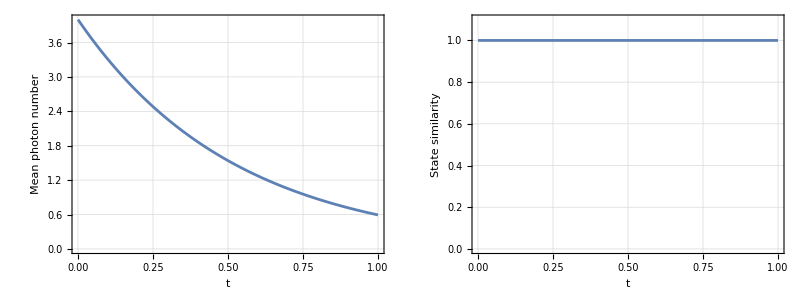
-Graphics-Evolution statistics of a coherent state

```mathematica
Labeled[
Grid[{{
ListLinePlot[Thread[{time,meanN}],],ListLinePlot[Thread[{time,qs}],]}}],
]
```

### Optical balance

Considering the following master equation, we look for balance between a driving field Hamiltonian and the single photon loss mechanism:

(ⅆ ρ)/ⅆt= -ⅈG[â+(â)^†,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

```mathematica
G = RandomReal[{1, 2}];
```

Random initial state:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize];
```

Hamiltonian definition associated with the master equation:

```mathematica
ℋ= QuantumOperator["Hamiltonian"[G(a+a["Dagger"]),{a},{γ}]];
```

Numerical evolution operator from t=0 to 3 :

```mathematica
expℋ =QuantumEvolve[ ℋ,None,{t,0,3}];
```

```mathematica
ρt := QuantumState[expℋ[t][ρ0],"Parameters"->t];
```

Steady state solution is a coherent state with amplitude α = -2ⅈ G/γ :

```mathematica
fidelities= Table[{t,QuantumSimilarity[ρt[t],coherent[-I 2G/γ],"Fidelity"]},{t,0,3,0.1}];
```

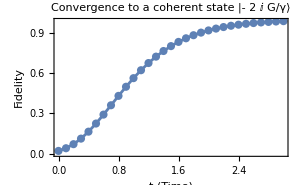

```mathematica
ListLinePlot[fidelities,]
```

For initial ρ̂(0) = |0⟩ ⟨0| evolves to coherent state | -ⅈ G t ⟩⟨- ⅈ G t | for short times, where the complex amplitude is independent of γ:

```mathematica
ρ0 = QuantumState["0",$FockSize];
```

```mathematica
time = Range[0,0.8,0.02];
qs = QuantumSimilarity[coherent[-I G #],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

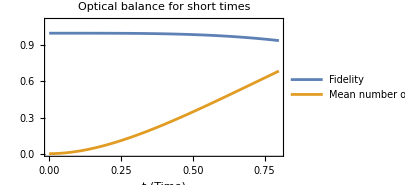

```mathematica
ListLinePlot[{Thread[{time,qs}],Thread[{time,meanN}]},]
```

### Jaynes-Cummings Model

Define the basis and the relevant operators:

```mathematica
SetFockSpaceSize[32];
atomBasis = QuantumBasis[{"e","g"}];
σplus =  QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];
a := AnnihilationOperator[{2}];
```

Free Hamiltonian  ℋ_0= ℏν(â)^†â+1/2 ℏωσ_z:

```mathematica
H0 = QuantumOperator[h ν SuperDagger[a]@a+1/2 h ω QuantumOperator["Z",atomBasis],"Parameters"->{ν,ω}];
```

Atom-field interaction term ℋ_I= ℏg(σ_+â+σ_-(â)^†):

```mathematica
H1=h g(σplus@a+σminus@SuperDagger[a]);
```

Going to the interaction picture at resonance, we get a time independent Hamiltonian:

```mathematica
HInteract=MatrixExp[I H0/h t]@H1@MatrixExp[-I H0/h t];
U=MatrixExp[-I HInteract[ν,ν]/h t];
```

Now we try different initial states

1. Rabi oscillations when the field is initially in a Fock state

```mathematica
ψ0 =QuantumState["1", atomBasis]// FockState[1];
ψt = U @ ψ0
```

-ⅈ sin(g t)e0+cos(g t)g1

Find the probability of the atom being in the excited state:

```mathematica
proj =QuantumOperator[{{1,0},{0,0}},atomBasis];
probE =(QuantumMeasurementOperator[proj]@ ψt)["Mean"];
```

Plot the result:

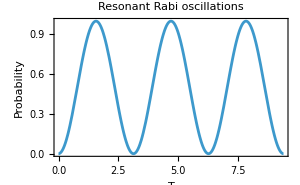

```mathematica
Plot[probE /. g->1 ,{t,0,3π},]
```

2. Collapse and revivals when the initial field state is a coherent state

|ψ_0⟩ = |g⟩|α⟩ with |α|=4

Define the initial state and evolve it (we use a random α):

```mathematica
α = 4 Exp[I RandomReal[{0, 2 π}]];
ψ0=QuantumState["1",atomBasis]//CoherentState[][α]["Normalize"];
ψt = QuantumState[U @ ψ0,"Parameters"->{g,t}];
```

Extracting the coefficients  c_e and c_g for all n as a function of time:

```mathematica
{cet[t_], cgt[t_]} = Values[(#["Dagger"]@ψt[1, t])["Amplitudes"]] & /@ atomBasis["BasisStates"];
```

Plotting the population inversion  W(t)=∑_n |c_(e,n)(t)|^2-|c_(g,n)(t)|^2

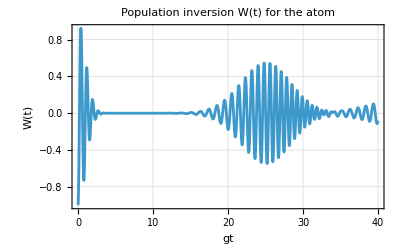

```mathematica
Plot[Total @(Abs[cet[t]]^2-Abs[cgt[t]]^2),{t,0,40},]
```

3. Atom "thermalization" (atom interacting with a thermal state field)

Atom initially in 1/(√2)(|g⟩+|e⟩) and field in a thermal state with n̄=5:

```mathematica
ρ0 = QuantumState["+",atomBasis]//ThermalState[5.];
```

Evolution of the density matrix  ρ(t) =Û(t) ρ(0) (Û)^†(t) (in the QuantumFramework we have a shortcut):

```mathematica
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
```

Reduced density matrix of the atom:

```mathematica
atomMatrix =Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]]//ComplexExpand//Simplify;
```

Plot  two components:

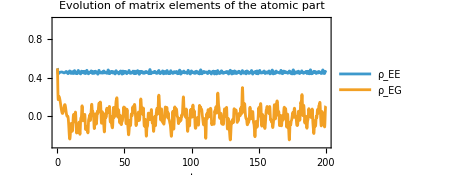

```mathematica
Plot[Evaluate[atomMatrix[[1,{1,2}]]],{t,0,200},]
```

Atom gets "thermalized", time average of the coherences → 0:

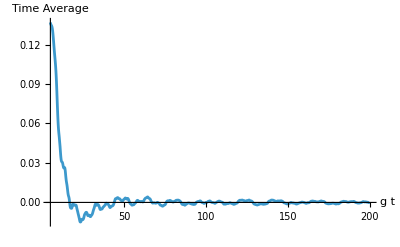

```mathematica
timeAverages = Integrate[(atomMatrix[[1,2]]),{t,0,tf}]/tf;
Plot[timeAverages,{tf,5,200},]
```

### Jaynes-Cummings with dissipation

Ĥ= ℏν(â)^†â+1/2 ℏωσ_z+ℏg(σ_+â+σ_-(â)^†)
ⅆρ/ⅆt= -ⅈ/ℏ[Ĥ, ρ]+ℒ_decay(ρ)+ℒ_loss(ρ)

where ℒ_decay,ℒ_loss are the master equation terms related to Lindblad jump operators L_1=√γ_1(σ_-⊗ ℐ) and L_2=√γ_2(ℐ ⊗ â), let's consider initial state |e⟩|n⟩ with n=2

```mathematica
SetFockSpaceSize[8];
ν = 10.;   (* field frequency *)
ω = 10.;   (* atomic frequency *)
gc = 15.; (* interaction coupling strength *)
ψ0 = QuantumState["0",atomBasis]//FockState[2];
```

Hamiltonian definition:

```mathematica
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Jump operators:

```mathematica
decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;
```

Helper definition to get the probability of finding the atom in the excited state:

```mathematica
atomProb[evolved_] := Table[{t, QuantumPartialTrace[evolved[t], {2}]["DensityMatrix"][[1, 1]] // Chop}, {t, 0, 1, 0.01}]
```

Calculating the evolution for different damping parameters γ=γ_1=γ_2, and saving the probability of finding the atom in the excited state:

```mathematica
probsE = Table[ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {x, x}]];
   evolved = QuantumEvolve[ℋ, ψ0, {t, 0, 1}];
   atomProb[evolved],
   {x, {0.8, 0.4, 0.2}}];
```

Damped Rabi oscillations:

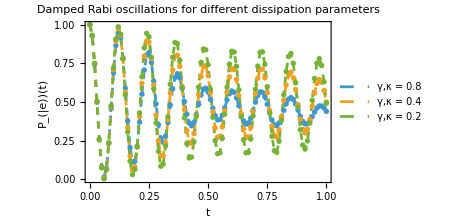

```mathematica
ListLinePlot[probsE,]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/SecondQuantization

### Keywords

Second Quantization

Fock Space

Quantum Optics